{{1,0.6348},{2,0.2964},{3,0.3002},{4,0.2983},{5,0.2964},{6,0.3041},{7,0.2945},{8,0.2964},{9,0.2945},{10,0.2945},{11,0.2906},{12,0.2925},{13,0.2926},{14,0.2906},{15,0.2964}}

{{1,0.6185},{2,0.3404},{3,0.3322},{4,0.3281},{5,0.3232},{6,0.32},{7,0.3158},{8,0.3125},{9,0.311},{10,0.3093},{11,0.3085},{12,0.3077},{13,0.3068},{14,0.306},{15,0.3052}}

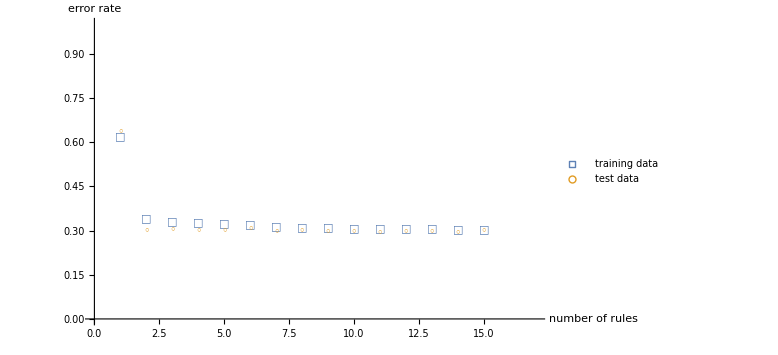

```mathematica
ges1c3000gen264popT
ges1c3000gen264popTr

ListPlot[{ges1c3000gen264popTr,ges1c3000gen264popT},ImageSize->Large,AxesOrigin->{0,0},AxesLabel->{"number of rules","error rate"},PlotRange->{{0,17},{0,1}},PlotLegends->Placed[{"training data","test data"},Right],PlotMarkers->{"□","◦"},PlotStyle->PointSize[Large]]
```

{{1,0.604},{2,0.329}}

{{1,0.599},{2,0.341}}

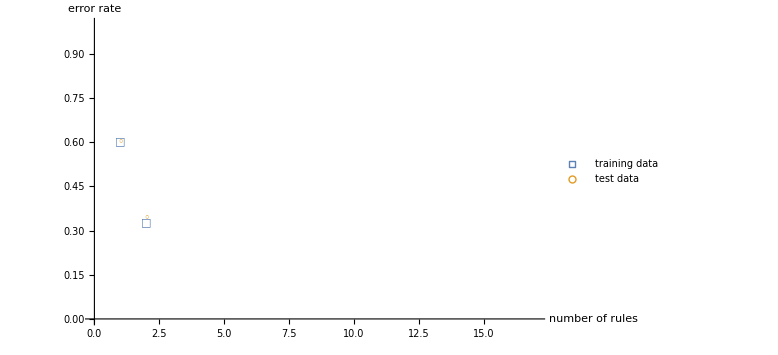

```mathematica
ges12c3000gen264popTr = {{1,1-0.396},{2,1-0.671}}
ges12c3000gen264popT = {{1,1-0.401},{2,1-0.659}}
ListPlot[{ges12c3000gen264popTr,ges12c3000gen264popT},ImageSize->Large,AxesOrigin->{0,0},AxesLabel->{"number of rules","error rate"},PlotRange->{{0,17},{0,1}},PlotLegends->Placed[{"training data","test data"},Right],PlotMarkers->{"□","◦"},PlotStyle->PointSize[Large]]
```

{{1,0.6104},{2,0.3495},{3,0.3421},{4,0.3323},{6,0.3314}}

{{1,0.654},{2,0.3423},{3,0.3404},{4,0.3384},{6,0.3576}}

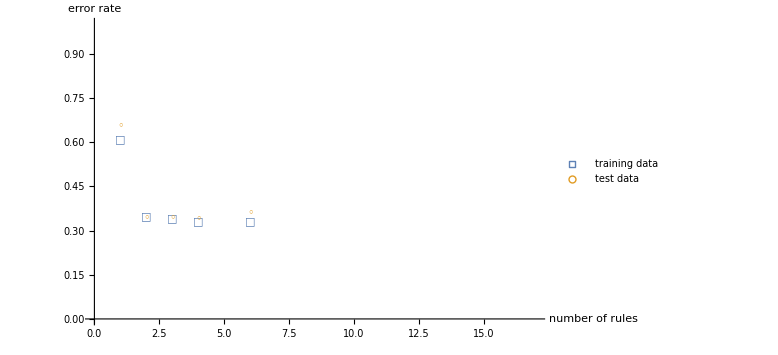

```mathematica
ges8c3000gen264popTr = {{1,1-0.3896},{2,1-0.6505},{3,1-0.6579},{4,1-0.6677},{6,1-0.6686}}
ges8c3000gen264popT = {{1,1-0.3460},{2,1-0.6577},{3,1-0.6596},{4,1-0.6616},{6,1-0.6424}}
ListPlot[{ges8c3000gen264popTr,ges8c3000gen264popT},ImageSize->Large,AxesOrigin->{0,0},AxesLabel->{"number of rules","error rate"},PlotRange->{{0,17},{0,1}},PlotLegends->Placed[{"training data","test data"},Right],PlotMarkers->{"□","◦"},PlotStyle->PointSize[Large]]
```

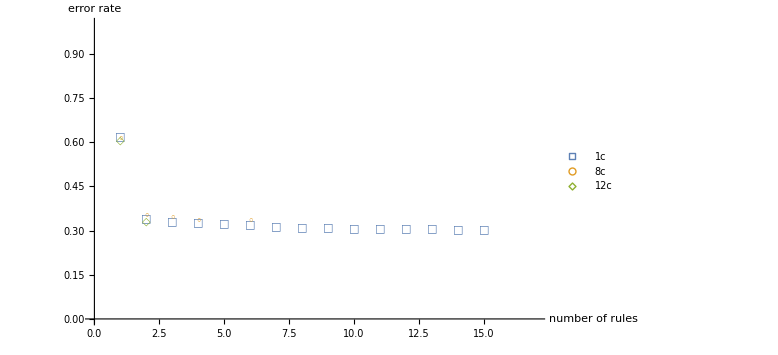

```mathematica
ListPlot[{ges1c3000gen264popTr,ges8c3000gen264popTr,ges12c3000gen264popTr},ImageSize->Large,AxesOrigin->{0,0},AxesLabel->{"number of rules","error rate"},PlotRange->{{0,17},{0,1}},PlotLegends->Placed[{"1c","8c","12c"},Right],PlotMarkers->{"□","◦","◇"},PlotStyle->PointSize[Large]]
```

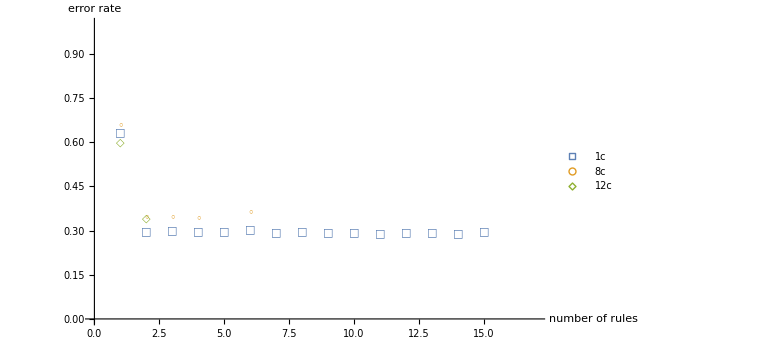

```mathematica
ListPlot[{ges1c3000gen264popT,ges8c3000gen264popT,ges12c3000gen264popT},ImageSize->Large,AxesOrigin->{0,0},AxesLabel->{"number of rules","error rate"},PlotRange->{{0,17},{0,1}},PlotLegends->Placed[{"1c","8c","12c"},Right],PlotMarkers->{"□","◦","◇"},PlotStyle->PointSize[Large]]
```